## DelaunayPairs-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51 (05 June 2017)) loaded Tue 6 Jun 2017 20:42:32
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

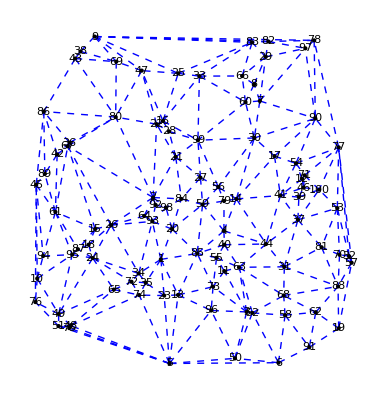

```mathematica
r:=RandomReal[{0, 10}]; 
v=Table[{r,r}, {100}];
de=DelaunayEdges[v];
Show[Graphics[{Blue, Dashed, Line/@de}], Graphics[Point/@v] , 
Graphics[MapThread[Text[ToString[#1], #2]&, {Range[Length[v]], v}]],
 BaseStyle-> {FontSize-> 16, FontColor-> Red}]
```

```mathematica
DelaunayPairs[v]
```

{{1,13},{1,20},{1,23},{1,34},{1,35},{1,85},{1,93},{2,21},{2,22},{2,26},{2,64},{2,67},{2,80},{2,84},{2,92},{2,98},{3,11},{3,50},{3,52},{3,63},{3,73},{3,96},{4,14},{4,40},{4,44},{4,59},{4,79},{4,85},{5,6},{5,13},{5,23},{5,48},{5,50},{5,51},{5,74},{5,75},{5,96},{6,50},{6,52},{6,58},{6,91},{7,8},{7,29},{7,30},{7,60},{7,90},{7,97},{8,29},{8,60},{8,66},{9,25},{9,38},{9,47},{9,69},{9,78},{9,82},{9,83},{10,45},{10,49},{10,76},{10,94},{10,95},{11,55},{11,63},{11,73},{12,41},{12,46},{12,54},{12,71},{13,23},{13,73},{13,85},{13,96},{14,17},{14,30},{14,41},{14,44},{14,56},{14,79},{15,18},{15,26},{15,61},{15,67},{15,87},{16,22},{16,25},{16,28},{16,33},{16,47},{16,99},{17,30},{17,41},{17,54},{17,90},{18,24},{18,26},{18,87},{19,57},{19,62},{19,88},{19,91},{20,59},{20,84},{20,85},{20,93},{20,98},{21,22},{21,27},{21,28},{21,84},{21,99},{22,28},{22,47},{22,80},{23,35},{23,74},{24,26},{24,34},{24,49},{24,65},{24,72},{24,87},{24,95},{25,33},{25,47},{25,83},{26,34},{26,64},{26,67},{26,93},{27,56},{27,59},{27,84},{27,99},{28,99},{29,66},{29,82},{29,83},{29,97},{30,56},{30,60},{30,90},{30,99},{31,37},{31,44},{31,63},{31,68},{31,81},{31,88},{32,53},{32,57},{32,70},{32,77},{33,60},{33,66},{33,83},{33,99},{34,35},{34,72},{34,93},{35,72},{35,74},{36,42},{36,67},{36,80},{36,86},{37,39},{37,41},{37,44},{37,53},{37,81},{37,100},{38,43},{38,69},{39,41},{39,46},{39,100},{40,44},{40,55},{40,63},{40,85},{41,44},{41,46},{41,54},{42,61},{42,67},{42,86},{42,89},{43,69},{43,80},{43,86},{44,63},{45,61},{45,76},{45,86},{45,89},{45,94},{46,71},{46,100},{47,69},{47,80},{48,49},{48,51},{48,65},{48,74},{48,75},{49,51},{49,65},{49,76},{49,95},{50,52},{50,96},{51,75},{51,76},{52,58},{52,63},{52,68},{53,70},{53,77},{53,81},{53,100},{54,71},{54,77},{54,90},{55,63},{55,73},{55,85},{56,59},{56,79},{56,99},{57,70},{57,77},{57,88},{58,62},{58,68},{58,91},{59,79},{59,84},{59,85},{60,66},{60,99},{61,67},{61,87},{61,89},{61,94},{61,95},{62,68},{62,88},{62,91},{63,68},{64,92},{64,93},{65,72},{65,74},{66,83},{67,80},{68,88},{69,80},{70,81},{70,88},{71,77},{71,100},{72,74},{73,85},{73,96},{77,78},{77,90},{77,100},{78,82},{78,90},{78,97},{80,86},{81,88},{82,83},{82,97},{84,98},{86,89},{87,95},{90,97},{92,93},{92,98},{93,98},{94,95}}